```mathematica
dim=3;
v={t[s], θ[s], ϕ[s]};
g={{1 ,0, 0},{0, -L^2, 0},{0, 0, -(L*Sin[θ[s]])^2}};
g//MatrixForm
```

(1 | 0 | 0
0 | -L^2 | 0
0 | 0 | -L^2 Sin[θ[s]]^2)

```mathematica
invg = Inverse[g]; 
invg // MatrixForm
```

(1 | 0 | 0
0 | -1/L^2 | 0
0 | 0 | -Csc[θ[s]]^2/L^2)

```mathematica
Γ=Table[
1/2*Sum[invg[[λ, ν]]*(D[g[[μ, ν]],v[[τ]]]+D[g[[ ν,τ]], v[[μ]]]-D[g[[τ, μ]], v[[ν]]]), {ν, 1, dim}],
 {λ, 1, dim},{μ, 1, dim}, {τ, 1, dim}];
Γ=Simplify[Γ];
Γ//MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
-Cos[θ[s]] Sin[θ[s]])
(0
0
0) | (0
0
Cot[θ[s]]) | (0
Cot[θ[s]]
0))

```mathematica
EQ= {
D[v[[1]],{s, 2}]+Sum[Γ[[1, λ, ν]]*D[v[[λ]], s]*D[v[[ν]], s],{λ, 1, dim},{ν, 1, dim}]==0,
D[v[[2]],{s, 2}]+Sum[Γ[[2, λ, ν]]*D[v[[λ]], s]*D[v[[ν]], s],{λ, 1, dim},{ν, 1, dim}]==0,
D[v[[3]],{s, 2}]+Sum[Γ[[3, λ, ν]]*D[v[[λ]], s]*D[v[[ν]], s],{λ, 1, dim},{ν, 1, dim}]==0
};
EQ//MatrixForm
```

(t''[s]==0
-Cos[θ[s]] Sin[θ[s]] ϕ'[s]^2+θ''[s]==0
2 Cot[θ[s]] θ'[s] ϕ'[s]+ϕ''[s]==0)

```mathematica
cond={
t[0]==0, t'[0]==0,
θ[0]==1.5, θ'[0]==1,
ϕ[0]==1.5, ϕ'[0]==1
};
sol=NDSolve[{EQ, cond}, {t, θ, ϕ}, {s, 0, 2*Pi}]
```

{{t→InterpolatingFunction[…],θ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

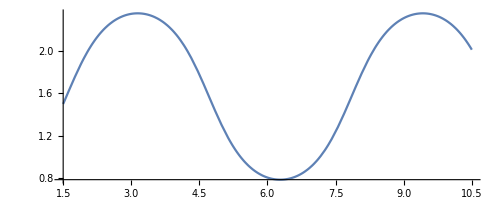

-Graphics3D-

```mathematica
a=ϕ[s]/.sol[[1,3]];
b=θ[s]/.sol[[1,2]];
ParametricPlot[{a, b}, {s, 0, 2*Pi}]
ParametricPlot3D[{Sin[b]*Cos[a], Sin[b]*Sin[a], Cos[b]}, {s, 0, 2*Pi}]
```

```mathematica
ParametricPlot3D[{{Sin[b]*Cos[a], Sin[b]*Sin[a], Cos[b]} , {Sin[u]*Cos[s], Sin[u]*Sin[s], Cos[u]}},
 {u, 0, Pi}, {s, 0, 2*Pi}, PlotStyle->{Thickness[0.01],Green}, PlotLabels->{"Geodetica"}]
```

-Graphics3D-